# Draw a Shape

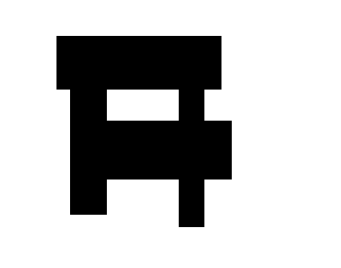
```mathematica
Shape=-Graphics-;
```

# ShapeMatrix and Grid Functions

```mathematica
Shape=Image[Shape,"Bit"];
Shape=Binarize[Shape];
Shape=ImageResize[Shape,70];
ShapeMat=ImageData[Shape,DataReversed->True];
ShapeMat=Transpose[ShapeMat];
```

## N_x and N_y are the number of grid points for the embedding itself.

```mathematica
Nx=Length[ShapeMat];
Ny=Length[ShapeMat[[1]]];
```

```mathematica
ShapeMatrix[x_,y_]:=If[(1≤x≤Nx)&&(1≤y≤Ny),ShapeMat[[x,y]],0]
```

## xEmbedding and yEmbedding are the dimensions of the embedding where we draw our shape (in meters). These values are picked such that we enforce dx = dy.

```mathematica
xEmbedding=1.6;
yEmbedding=(Ny/Nx)*xEmbedding;
```

```mathematica
dx=N[xEmbedding/Nx];
dy=N[yEmbedding/Ny];
```

## Grid Functions for identifying various regions:

## InsideQ is a test of being inside the shape. OutsideQ is a test of being outside the shape.

```mathematica
InsideQ[i_,j_]:=ShapeMatrix[i,j]==1;
OutsideQ[i_,j_]:=ShapeMatrix[i,j]==0;
```

## SurroundedQ tests whether a point is surrounded by other points which are in the shape.

```mathematica
SurroundedQ[i_,j_]:= ShapeMatrix[i,j]+ShapeMatrix[i,j+1]+ShapeMatrix[i,j-1]+ShapeMatrix[i-1,j]+ShapeMatrix[i-1,j+1]+ShapeMatrix[i-1,j-1]+ShapeMatrix[i+1,j]+ShapeMatrix[i+1,j+1]+ShapeMatrix[i+1,j-1]==9;
```

## top and bottom BoundaryQ test if a point is in the top or the bottom boundary regions

```mathematica
TopBoundaryQ[i_,j_]:=SurroundedQ[i,j]&&((ShapeMatrix[i,j+1]==1&&ShapeMatrix[i,j+2]==0)||ShapeMatrix[i-1,j+2]==0||ShapeMatrix[i+1,j+2]==0);
BottomBoundaryQ[i_,j_]:=SurroundedQ[i,j]&&((ShapeMatrix[i,j-1]==1&&ShapeMatrix[i,j-2]==0)||ShapeMatrix[i-1,j-2]==0||ShapeMatrix[i+1,j-2]==0);
```

```mathematica
tbBoundaryQ[i_,j_]:=TopBoundaryQ[i,j]||BottomBoundaryQ[i,j];
```

## left and right BoundaryQ test if a point is in the left or right boundary regions

```mathematica
LeftBoundaryQ[i_,j_]:=SurroundedQ[i,j]&&((ShapeMatrix[i-1,j]==1&&ShapeMatrix[i-2,j]==0)|| ShapeMatrix[i-2,j-1]==0||ShapeMatrix[i-2,j+1]==0);
RightBoundaryQ[i_,j_]:=SurroundedQ[i,j]&&((ShapeMatrix[i+1,j]==1&&ShapeMatrix[i+2,j]==0)|| ShapeMatrix[i+2,j-1]==0||ShapeMatrix[i+2,j+1]==0);
```

```mathematica
lrBoundaryQ[i_,j_]:=LeftBoundaryQ[i,j]||RightBoundaryQ[i,j];
```

```mathematica
sidesQ[i_,j_]:=tbBoundaryQ[i,j]||lrBoundaryQ[i,j];
```

```mathematica
ThreeQ[i_,j_]:=(ShapeMatrix[i,j+1]+ShapeMatrix[i,j-1]+ShapeMatrix[i-1,j]+ShapeMatrix[i-1,j+1]+ShapeMatrix[i-1,j-1]+ShapeMatrix[i+1,j]+ShapeMatrix[i+1,j+1]+ShapeMatrix[i+1,j-1]==3);
SevenQ[i_,j_]:=(ShapeMatrix[i,j+1]+ShapeMatrix[i,j-1]+ShapeMatrix[i-1,j]+ShapeMatrix[i-1,j+1]+ShapeMatrix[i-1,j-1]+ShapeMatrix[i+1,j]+ShapeMatrix[i+1,j+1]+ShapeMatrix[i+1,j-1]==7);
```

## Below are the normal corner tests. nTLC stands for the normal top left corner nBRC stands for the normal bottom right corner

```mathematica
nTLC[i_,j_]:=ThreeQ[i-1,j+1]&&ShapeMatrix[i-1,j]==1&&ShapeMatrix[i,j+1]==1;
nBLC[i_,j_]:=ThreeQ[i-1,j-1]&&ShapeMatrix[i-1,j]==1&&ShapeMatrix[i,j-1]==1;
nTRC[i_,j_]:=ThreeQ[i+1,j+1]&&ShapeMatrix[i+1,j]==1&&ShapeMatrix[i,j+1]==1;
nBRC[i_,j_]:=ThreeQ[i+1,j-1]&&ShapeMatrix[i+1,j]==1&&ShapeMatrix[i,j-1]==1;
```

```mathematica
normalCornersQ[i_,j_]:=nTLC[i,j]||nBLC[i,j]||nTRC[i,j]||nBRC[i,j];
```

## Below are the combined corner tests. cTLC stands for the combined top left corner cBRC stands for the combined bottom right corner

```mathematica
cTLC[i_,j_]:=SevenQ[i-1,j+1]&&ShapeMatrix[i-2,j]==1&&ShapeMatrix[i,j+2]==1;
cBLC[i_,j_]:=SevenQ[i-1,j-1]&&ShapeMatrix[i-2,j]==1&&ShapeMatrix[i,j-2]==1;
cTRC[i_,j_]:=SevenQ[i+1,j+1]&&ShapeMatrix[i+2,j]==1&&ShapeMatrix[i,j+2]==1;
cBRC[i_,j_]:=SevenQ[i+1,j-1]&&ShapeMatrix[i+2,j]==1&&ShapeMatrix[i,j-2]==1;
```

```mathematica
combinedCornersQ[i_,j_]:=cTLC[i,j]||cBLC[i,j]||cTRC[i,j]||cBRC[i,j];
```

```mathematica
cornerBoundaryQ[i_,j_]:=SurroundedQ[i,j]&&normalCornersQ[i,j]||SurroundedQ[i,j]&&combinedCornersQ[i,j];
```

```mathematica
onBoundaryQ[i_,j_]:=cornerBoundaryQ[i,j]||lrBoundaryQ[i,j]||tbBoundaryQ[i,j];
```

# ∇^4 and ∂_xx , ∂_xy, and ∂_yy Finite Difference Matrices

```mathematica
v=0.35;(*Poisson's ratio*)
```

```mathematica
g[x_,y_] := x+(y - 1)*Nx ;
```

## The D4 matrices are for the transverse and in-plane eigenmodes. The ∂_xx , ∂_xy and ∂_yy matrices are for calculating the coupling coefficients later on in H and E.

∂_xx

## DXXmat is the double - x - derivative finite difference matrix which is used for calculating the H and E coefficients.

```mathematica
DXXmat[Nx_, Ny_, dx_, dy_] := Module[{retmat, i,index, indey,ij,ip1j,im1j},
retmat = Table[0.0,{i,1,Nx Ny},{j,1,Nx Ny}];

InGrid[pt_]:=1≤pt[[1]]≤Nx&&1≤pt[[2]]≤Ny;
Points[i_,j_]:={{i+1,j},{i,j},{i-1,j}};
Contributions={1/dx^2,-2/dx^2,1/dx^2};
InOrOut[surr_]:=Boole[Table[InGrid[surr[[i]]],{i,1,Length[surr]}]];

For[indey = 1, indey ≤ Ny, indey = indey+1,
For[index = 1, index ≤ Nx, index = index+1,

ij=g[index,indey];
ip1j=g[index+1,indey];
im1j=g[index-1,indey];

Terms={ip1j,ij,im1j};
Status=InOrOut[Points[index,indey]];

For[i=1,i≤3,i+=1,If[Status[[i]]≠0,retmat[[ij,Terms[[i]]]]+=Contributions[[i]]]];

];
];
Return[retmat];
]
```

∂_yy

## DYYmat is the double-y-derivative finite difference matrix which is used for calculating the H and E coefficients.

```mathematica
DYYmat[Nx_, Ny_, dx_, dy_] := Module[{retmat, i,index, indey,ij,ijp1,ijm1},

retmat = Table[0.0,{i,1,Nx Ny},{j,1,Nx Ny}];

InGrid[pt_]:=1≤pt[[1]]≤Nx&&1≤pt[[2]]≤Ny;
Points[i_,j_]:={{i,j+1},{i,j},{i,j-1}};
Contributions={1/dy^2,-2/dy^2,1/dy^2};
InOrOut[surr_]:=Boole[Table[InGrid[surr[[i]]],{i,1,Length[surr]}]];

For[indey = 1, indey ≤ Ny, indey = indey+1,
For[index = 1, index ≤ Nx, index = index+1,

ij=g[index,indey];
ijp1=g[index,indey+1];
ijm1=g[index,indey-1];

Terms={ijp1,ij,ijm1};
Status=InOrOut[Points[index,indey]];

For[i=1,i≤3,i+=1,If[Status[[i]]≠0,retmat[[ij,Terms[[i]]]]+=Contributions[[i]]]];

];
];
Return[retmat];
]
```

∂_xy

## DXYmat is the xy-cross-derivative finite difference matrix which is used for calculating the H and E coefficients.

```mathematica
DXYmat[Nx_, Ny_, dx_, dy_] := Module[{retmat, i,index, indey,ij,ip1jp1,ip1jm1,im1jp1,im1jm1},

retmat = Table[0.0,{i,1,Nx Ny},{j,1,Nx Ny}];

InGrid[pt_]:=1≤pt[[1]]≤Nx&&1≤pt[[2]]≤Ny;
Points[i_,j_]:={{i+1,j+1},{i+1,j-1},{i-1,j+1},{i-1,j-1}};
Contributions={1./(4dx dy),-1./(4dx dy),-1./(4dx dy),1./(4dx dy)};
InOrOut[surr_]:=Boole[Table[InGrid[surr[[i]]],{i,1,Length[surr]}]];

For[indey = 1, indey ≤ Ny, indey = indey+1,
For[index = 1, index ≤ Nx, index = index+1,

ij=g[index,indey];
ip1jp1=g[index+1,indey+1];
ip1jm1=g[index+1,indey-1];
im1jp1=g[index-1,indey+1];
im1jm1=g[index-1,indey-1];

Terms={ip1jp1,ip1jm1,im1jp1,im1jm1};
Status=InOrOut[Points[index,indey]];

For[i=1,i≤4,i+=1,If[Status[[i]]≠0,retmat[[ij,Terms[[i]]]]+=Contributions[[i]]]];

];
];
Return[retmat];
]
```

D4 transverse

## D4 is the matrix used to calculate the discrete transverse eigenmodes of oscillation

```mathematica
D4[Nx_, Ny_, dx_, dy_] := Module[{retmat, index, indey,i,LRconstant,TBconstant,inORout,bPts,d4Pts,d4C,leftC,rightC,topC,bottomC,nTLCC,nTRCC,nBLCC,nBRCC,cTLCC,cTRCC,cBLCC,cBRCC,InteriorUpdate,PiecewiseSides,PiecewiseCorners},

retmat = Table[0.0,{i,1,Nx Ny},{j,1,Nx Ny}];
inORout[surr_]:=Boole[Table[InsideQ[surr[[i]][[1]],surr[[i]][[2]]],{i,1,Length[surr]}]];

(*∇^4 approximation:*)
d4Pts[idx_,idy_]:={{idx+1,idy+1},{idx+1,idy},{idx+1,idy-1},{idx,idy+1},{idx,idy},{idx,idy-1},{idx-1,idy+1},{idx-1,idy},{idx-1,idy-1},{idx-2,idy},{idx+2,idy},{idx,idy-2},{idx,idy+2}};d4C={1./(dx^2 dy^2), -4./dx^4-2./(dx^2 dy^2), 1./(dx^2 dy^2),-4./dy^4 + -2./(dx^2 dy^2), 6./ dx^4+4./(dx^2 dy^2)+6./ dy^4 ,-4./dy^4-2./(dx^2 dy^2), 1./(dx^2 dy^2), -4./dx^4 -2./(dx^2 dy^2),1./(dx^2 dy^2),1./(dx)^4 ,1./dx^4,1./dy^4,1./dy^4};

(*boundary condition approximations*)
bPts[idx_,idy_]:={{idx-1,idy},{idx+1,idy},{idx,idy-1},{idx,idy+1}};

(*boundary sides*)
LRconstant=(2./(dx)^2+2v/(dy)^2)^(-1);
TBconstant=(2./(dy)^2+2v/(dx)^2)^(-1);
leftC=LRconstant*{0,1./(dx)^2,v/(dy)^2,v/(dy)^2};
rightC=LRconstant*{1./(dx)^2,0,v/(dy)^2,v/(dy)^2};
topC=TBconstant*{1./(dy)^2,1./(dy)^2,v/(dx)^2,0};
bottomC=TBconstant*{1./(dy)^2,1./(dy)^2,0,v/(dx)^2};

(*boundary corners*)
nTLCC=1/2(topC+leftC);
nTRCC=1/2(topC+rightC);
nBLCC=1/2(bottomC+leftC);
nBRCC=1/2(bottomC+rightC);

cTLCC=nTLCC;
cTRCC=nTRCC;
cBLCC=nBLCC;
cBRCC=nBRCC;

(*accuracy of method*)

InteriorUpdate[i_,j_]:=Module[{ij,im2j,im1j,ip1j,ip2j,ijm2,ijm1,ijp1,ijp2, ip1jp1,ip1jm1,im1jp1,im1jm1,ii,terms,status},
ip1jp1=g[i+1,j+1];
ip1j=g[i+1,j];
ip1jm1=g[i+1,j-1];

ijp1=g[i,j+1];
ij=g[i,j];
ijm1=g[i,j-1];

im1jp1=g[i-1,j+1];
im1j=g[i-1,j];
im1jm1=g[i-1,j-1];

im2j=g[i-2,j];
ip2j=g[i+2,j];

ijm2=g[i,j-2];
ijp2=g[i,j+2];

terms={ip1jp1,ip1j,ip1jm1,ijp1,ij,ijm1,im1jp1,im1j, im1jm1,im2j,ip2j,ijm2,ijp2};
status=inORout[d4Pts[i,j]];

For[ii=1,ii≤Length[terms],ii++,If[status[[ii]]≠0,retmat[[ij,terms[[ii]]]]+=d4C[[ii]]]];
];

PiecewiseSides[i_,j_]:=Module[{ij,im1j,ip1j,ijm1,ijp1,bTerms,bStatus,ii},
ij=g[i,j];
im1j=g[i-1,j];
ip1j=g[i+1,j];
ijm1=g[i,j-1];
ijp1=g[i,j+1];

bTerms={im1j,ip1j,ijm1,ijp1};
bStatus=inORout[bPts[i,j]];

Piecewise[{{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*topC[[ii]]]],TopBoundaryQ[i,j]},{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*bottomC[[ii]]]],BottomBoundaryQ[i,j]},{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*leftC[[ii]]]],LeftBoundaryQ[i,j]},{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*rightC[[ii]]]],RightBoundaryQ[i,j]}}];
];

PiecewiseCorners[i_,j_]:=Module[{ij,im1j,ip1j,ijm1,ijp1,bTerms,bStatus,ii},
ij=g[i,j];
im1j=g[i-1,j];
ip1j=g[i+1,j];
ijm1=g[i,j-1];
ijp1=g[i,j+1];

bTerms={im1j,ip1j,ijm1,ijp1};
bStatus=inORout[bPts[i,j]];

Piecewise[{{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*nTLCC[[ii]]]],nTLC[i,j]},
{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*nTRCC[[ii]]]],nTRC[i,j]},
{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*nBLCC[[ii]]]],nBLC[i,j]},
{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*nBRCC[[ii]]]],nBRC[i,j]},
{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*cTLCC[[ii]]]],cTLC[i,j]},
{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*cTRCC[[ii]]]],cTRC[i,j]},
{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*cBLCC[[ii]]]],cBLC[i,j]},
{For[ii=1,ii≤Length[bTerms],ii+=1,If[bStatus[[ii]]≠0,retmat[[ij,bTerms[[ii]]]]+=bStatus[[ii]]*cBRCC[[ii]]]],cBRC[i,j]}
}];

];


For[index=1,index≤Nx,index++,
For[indey=1,indey≤Ny,indey++,
If[SurroundedQ[index,indey],
If[onBoundaryQ[index,indey],
If[cornerBoundaryQ[index,indey],PiecewiseCorners[index,indey],PiecewiseSides[index,indey]];,
InteriorUpdate[index,indey];]
];
];
];

Return[retmat];
];
```

D4 in-plane

## D4inPlane is the matrix used to calculate the discrete in-plane eigenmodes of oscillation

```mathematica
D4InPlane[Nx_, Ny_, dx_, dy_] := Module[{retmat, index, indey,ij,im2j,im1j,ip1j,ip2j,ijm2,ijm1,ijp1,ijp2, ip1jp1,ip1jm1,im1jp1,im1jm1,coverage1,coverage2,coverage3,coverage4,in,out,bdry,inORout,d4Pts,d4C,terms,status,i},

retmat = Table[0.0,{i,1,Nx Ny},{j,1,Nx Ny}];
inORout[surr_]:=Boole[Table[InsideQ[surr[[i]][[1]],surr[[i]][[2]]],{i,1,Length[surr]}]];

(*∇^4 approximation:*)
d4Pts[idx_,idy_]:={{idx+1,idy+1},{idx+1,idy},{idx+1,idy-1},{idx,idy+1},{idx,idy},{idx,idy-1},{idx-1,idy+1},{idx-1,idy},{idx-1,idy-1},{idx-2,idy},{idx+2,idy},{idx,idy-2},{idx,idy+2}};d4C={1./(dx^2 dy^2), -4./dx^4-2./(dx^2 dy^2), 1./(dx^2 dy^2),-4./dy^4 + -2./(dx^2 dy^2), 6./ dx^4+4./(dx^2 dy^2)+6./ dy^4 ,-4./dy^4-2./(dx^2 dy^2), 1./(dx^2 dy^2), -4./dx^4 -2./(dx^2 dy^2),1./(dx^2 dy^2),1./(dx)^4 ,1./dx^4,1./dy^4,1./dy^4};

For[index=1,index≤Nx,index++,
For[indey=1,indey≤Ny,indey++,
If[SurroundedQ[index,indey]&&onBoundaryQ[index,indey]==False,
ip1jp1=g[index+1,indey+1];
ip1j=g[index+1,indey];
ip1jm1=g[index+1,indey-1];

ijp1=g[index,indey+1];
ij=g[index,indey];
ijm1=g[index,indey-1];

im1jp1=g[index-1,indey+1];
im1j=g[index-1,indey];
im1jm1=g[index-1,indey-1];

im2j=g[index-2,indey];
ip2j=g[index+2,indey];

ijm2=g[index,indey-2];
ijp2=g[index,indey+2];


terms={ip1jp1,ip1j,ip1jm1,ijp1,ij,ijm1,im1jp1,im1j, im1jm1,im2j,ip2j,ijm2,ijp2};
status=inORout[d4Pts[index,indey]];

For[i=1,i≤Length[terms],i++,If[status[[i]]≠0,retmat[[ij,terms[[i]]]]+=d4C[[i]]];
];

];
];
];
Return[retmat];
];
```

# Plotting Functions

## These functions can be used to plot the eigenmodes on the plate desired (as opposed to plotting the eigenmode across the embedding).

```mathematica
PlotPoisson[invec_, Nx_,dx_, Ny_, dy_,conum_:20] := Module[{g, Datatable,retplot},
g[n_,m_] := (m - 1)*Nx + n;
Datatable= Table[{ii dx, jj dy, invec[[ g[ii,jj] ]]},{ii,1, Nx}, {jj,1,Ny}];
Datatable = Partition[Flatten[Datatable],3];
retplot = ListContourPlot[Datatable,Contours-> conum,PlotRange->All];
Return[retplot];
]
```

```mathematica
PlotPoisson3D[invec_, Nx_,dx_, Ny_, dy_] := Module[{g, Datatable,retplot},
g[n_,m_] := (m - 1)*Nx + n;
Datatable= Table[{ii,jj,invec[[ g[ii,jj] ]]},{ii,1, Nx}, {jj,1,Ny}];
Datatable = Partition[Flatten[Datatable],3];
retplot = ListPlot3D[Datatable,RegionFunction->Function[{x,y,z},InsideQ[Round[x],Round[y]]],PlotRange-> All];
Return[retplot];
]
```

# Eigenvectors & Eigenvalues

## Specify the number of eigenmodes (transverse and longitudinal) desired.

```mathematica
Nϕ=10;
Nψ=Nϕ;
```

## Transverse

```mathematica
D4mat=D4[Nx,Ny,dx,dy];
```

```mathematica
{iVals,iVecs}= Eigensystem[D4mat];
```

```mathematica
iVals=Reverse[iVals];
iVecs=Reverse[iVecs];
```

## The Select function call below filters all of the eigenfunctions whose associated eigenfrequencies are too small to be audible (usually we’re filtering frequencies less than 1 Hz).

```mathematica
wVals=Select[iVals,Re[#]>5&];
```

```mathematica
λ=Re[wVals];
```

```mathematica
ϕ=iVecs[[Length[iVecs]+1-Length[wVals];;]];
```

```mathematica
λ=λ[[;;Nϕ]];
ϕ=ϕ[[;;Nϕ]];
```

```mathematica
PlotPoisson3D[ϕ[[1]],Nx,dx,Ny,dy]
```

-Graphics3D-

## Longitudinal

```mathematica
fD4mat=D4InPlane[Nx,Ny,dx,dy];
```

```mathematica
{fVals,fVecs}= Eigensystem[fD4mat];
```

```mathematica
fVals=Reverse[fVals];
fVecs=Reverse[fVecs];
```

```mathematica
fVals=Select[fVals,Re[#]>1&];
```

```mathematica
ξ=Re[fVals];
```

```mathematica
ξ=Sqrt[Sqrt[ξ]];
ψ=fVecs[[Length[fVecs]+1-Length[fVals];;]];
```

```mathematica
ξ=ξ[[;;Nψ]];
ψ=ψ[[;;Nψ]];
```

```mathematica
PlotPoisson3D[ψ[[3]],Nx,dx,Ny,dy]
```

-Graphics3D-

# Coupling Coefficients (H & E)

```mathematica
Export[NotebookDirectory[]<>"TransverseEvals.m",λ];
Export[NotebookDirectory[]<>"xi.m",ξ];
```

## D2X, D2Y and DXY are the finite difference matrices used for calculating the coupling coefficients

```mathematica
D2X=SparseArray[DXXmat[Nx, Ny, dx, dy]];
D2Y=SparseArray[DYYmat[Nx, Ny, dx, dy]];
DXY=SparseArray[DXYmat[Nx, Ny, dx, dy]];
```

```mathematica
L[α_,β_]:=(D2X.α)*(D2Y.β)+(D2Y.α)*(D2X.β)-2(DXY.α)*(DXY.β);
SurfaceIntegral[a_,b_]:=(dx dy)a.b;
```

```mathematica
ϕ==Re[ϕ]
ψ==Re[ψ]
```

True

True

```mathematica
ϕ=Re[ϕ];
ψ=Re[ψ];
```

```mathematica
Export[NotebookDirectory[]<>"phi.m",ϕ];
Export[NotebookDirectory[]<>"psi.m",ψ];
```

## The norm of a eigenfunction is the square root of its inner product with itself. Here the inner product is a discretized surface integral over the space of the plate. Note that all of these eigenvectors have the same norm because the output of the EigenSystem function forms an orthonormal set.

```mathematica
norm[x_]:=Sqrt[SurfaceIntegral[x,x]]
```

```mathematica
NormPhi=norm[ϕ[[1]]];
NormPsi=norm[ψ[[1]]];
```

```mathematica
NormFactor=NormPhi*NormPhi*NormPsi;
```

```mathematica
H[i_,j_,k_]:=SurfaceIntegral[ψ[[k]],L[ϕ[[i]],ϕ[[j]]]]/NormFactor;
Et[i_,j_,s_]:=SurfaceIntegral[ϕ[[s]],L[ϕ[[i]],ψ[[j]]]]/NormFactor;
```

## Using these ParallelTable commands provide a nice speed-up when the number of eigenmodes is sufficiently large.

```mathematica
HTable=ParallelTable[Flatten[Table[H[i,j,s],{i,1,Nϕ},{j,1,Nψ}]],{s,1,Nϕ}];
```

```mathematica
ETable=ParallelTable[Flatten[Table[Et[i,j,s],{i,1,Nϕ},{j,1,Nψ}]],{s,1,Nϕ}];
```

```mathematica
Export[NotebookDirectory[]<>"HTable.m",HTable];
```

```mathematica
Export[NotebookDirectory[]<>"ETable.m",ETable];
```

```mathematica
details={Nx,Ny,dx,dy,xEmbedding,yEmbedding,Nϕ,Nψ};
```

```mathematica
Export[NotebookDirectory[]<>"details.m",details];
```